```mathematica
ClearAll[a,b,c,d,bgrid,x,y,omgrid,test,lent,om,b1,s3]
test= Import["/home/manvendra/post_doc_ahduni/sim/mod_grav/plot_data/s0_plots/test.txt","Table"];
bgrid= Import["/home/manvendra/post_doc_ahduni/sim/mod_grav/plot_data/s0_plots/s3_z0_bgrid.txt","Table"];

omgrid= Import["/home/manvendra/post_doc_ahduni/sim/mod_grav/plot_data/s0_plots/s3_z0_omgrid.txt","Table"];
```

```mathematica
t = Join[bgrid,omgrid];
lent =Length[t];
```

```mathematica
om = Table[t[[k,1]],{k,lent}];
b1 = Table[t[[k,2]],{k,lent}];
s3 =  Table[t[[k,3]],{k,lent}];
```

```mathematica
FindFit[t,a+b*(x^c -1)+d*x*y^2+f*x*(1+y^2+y^3),{a,b,c,d,f},{x,y},WorkingPrecision->MachinePrecision]
prd = a+b*(om^c -1)+d*om*b1^2+f*om*(1+b1^2+b1^3)/.%;
```

{a→4.76987,b→-0.127787,c→0.820854,d→-0.184214,f→0.0613666}

```mathematica
diff = (prd -s3)*100/prd;
asrd = RootMeanSquare[diff]
mrd = Max[Abs[diff]]
```

0.354722

1.59653

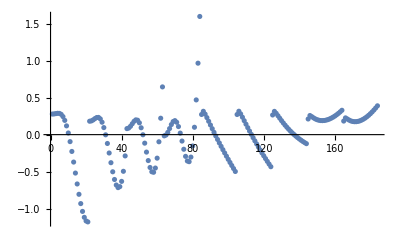

```mathematica
ListPlot[diff]
```

```mathematica
FindFit[t,a+b*(x^c -1)+d*x*y+f(1+y^2),{a,b,c,d,f},{x,y}]
```

{a→4.82293,b→-0.0135438,c→3.79463,d→-0.103554,f→0.0233212}

```mathematica
$MachinePrecision
```

15.9546

```mathematica
Limit[x^3/x,{x,y}->{0,0}]
```

0